```mathematica
SetDirectory[NotebookDirectory[]];
<< "OpticSimulate.wl"
```

```mathematica
elems = {ConvexLens[0,0,0,1,2]};
elems = GenerateASTs[elems];
SimulBeam[{4,3},elems,{0,1,0.0001,-0.01},75]
```

{{0.0001,0.99},{0.0002,0.98},{0.0003,0.97},{0.0004,0.96},{0.0005,0.95},{0.0006,0.94},{0.0007,0.93},{0.0008,0.92},{0.0009,0.91},{0.001,0.9},{0.0011,0.89},{0.0012,0.88},{0.0013,0.87},{0.0014,0.86},{0.0015,0.85},{0.0016,0.84},{0.0017,0.83},{0.0018,0.82},{0.0019,0.81},{0.002,0.8},{0.0021,0.79},{0.0022,0.78},{0.0023,0.77},{0.0024,0.76},{0.0025,0.75},{0.0026,0.74},{0.0027,0.73},{0.0028,0.72},{0.0029,0.71},{0.003,0.7},{0.0031,0.69},{0.0032,0.68},{0.0033,0.67},{0.0034,0.66},{0.0035,0.65},{0.0036,0.64},{0.0037,0.63},{0.0038,0.62},{0.0039,0.61},{0.004,0.6},{0.0041,0.59},{0.0042,0.58},{0.0043,0.57},{0.0044,0.56},{0.0045,0.55},{0.0046,0.54},{0.0047,0.53},{0.0048,0.52},{0.0049,0.51},{0.005,0.5},{0.0051,0.49},{0.0052,0.48},{0.0053,0.47},{0.0054,0.46},{0.0055,0.45},{0.0056,0.44},{0.0057,0.43},{0.0058,0.42},{0.0059,0.41},{0.006,0.4},{0.0061,0.39},{0.0062,0.38},{0.0063,0.37},{0.0064,0.36},{0.0065,0.35},{0.0066,0.34},{0.0067,0.33},{0.0068,0.32},{0.0069,0.31},{0.007,0.3},{0.0071,0.29},{0.0072,0.28},{0.0073,0.27},{0.00706461,0.26},{0.0169799,0.261859}}

```mathematica
OpticRenderStatic[{4,3},{BasicMirror[0,0,0,2]}]
```

-Graphics-

```mathematica
OpticRenderStatic[{4,3},{ConvexLens[0,0,0,3/2,3]}]
```

outgoing -0.294524 1.44285 -1.73738 ArcSin[0.555556 Sin[ToPolarCoordinates[{9.97363×10^-19+0.00935558 ⅈ,-0.0162882+5.72864×10^-19 ⅈ}]⟦2⟧-ToPolarCoordinates[{0.248011+0.00511591 ⅈ,1}]⟦2⟧]] -0.547865

outgoing -0.57981 1.81583 -2.39564 -0.57981 -1.22161

Less::nord: Invalid comparison with 1.08327+0.0140334 ⅈ attempted.

Greater::nord: Invalid comparison with 1.08327+0.0140334 ⅈ attempted.

Less::nord: Invalid comparison with -0.142072+8.59296×10^-19 ⅈ attempted.

Greater::nord: Invalid comparison with -0.142072+8.59296×10^-19 ⅈ attempted.

LessEqual::nord: Invalid comparison with 1.19346+0.0304039 ⅈ attempted.

Greater::nord: Invalid comparison with 1.19346+0.0304039 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

ToPolarCoordinates::bdpt: Evaluation point {9.97363×10^-19+0.00935558 ⅈ,-0.0162882+5.72864×10^-19 ⅈ} is not a valid set of Cartesian coordinates.

Part::partw: Part 2 of ToPolarCoordinates[{9.97363×10^-19+0.00935558 ⅈ,-0.0162882+5.72864×10^-19 ⅈ}] does not exist.

ToPolarCoordinates::bdpt: Evaluation point {0.248011+0.00511591 ⅈ,1} is not a valid set of Cartesian coordinates.

Part::partw: Part 2 of ToPolarCoordinates[{0.248011+0.00511591 ⅈ,1}] does not exist.

outgoing ToPolarCoordinates[{9.97363×10^-19+0.00935558 ⅈ,-0.0162882+5.72864×10^-19 ⅈ}]⟦2⟧ ToPolarCoordinates[{0.248011+0.00511591 ⅈ,1}]⟦2⟧ ToPolarCoordinates[{9.97363×10^-19+0.00935558 ⅈ,-0.0162882+5.72864×10^-19 ⅈ}]⟦2⟧-ToPolarCoordinates[{0.248011+0.00511591 ⅈ,1}]⟦2⟧ -1.5708+0.654033 ⅈ 0.555556 Sin[ToPolarCoordinates[{9.97363×10^-19+0.00935558 ⅈ,-0.0162882+5.72864×10^-19 ⅈ}]⟦2⟧-ToPolarCoordinates[{0.248011+0.00511591 ⅈ,1}]⟦2⟧]

ToPolarCoordinates::bdpt: Evaluation point {0.248011+0.00511591 ⅈ,1.} is not a valid set of Cartesian coordinates.

General::stop: Further output of ToPolarCoordinates::bdpt will be suppressed during this calculation.

Part::partw: Part 2 of ToPolarCoordinates[{0.248011+0.00511591 ⅈ,1.}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ArrayReshape::listrp: List or SparseArray or structured array expected at position 1 in ArrayReshape[res$234622,{2,2}].

ArrayReshape::listrp: List or SparseArray or structured array expected at position 1 in ArrayReshape[res$234627,{2,2}].

ArrayReshape::listrp: List or SparseArray or structured array expected at position 1 in ArrayReshape[res$234634,{2,2}].

General::stop: Further output of ArrayReshape::listrp will be suppressed during this calculation.

1

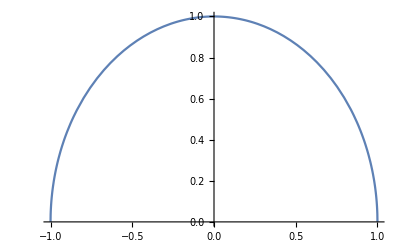

```mathematica
r = 1
exp:=Sqrt[r^2-x^2]-Sqrt[r^2-1^2]
Plot[exp, {x,-1,1}]
(* RegionPlot[0<=y<=exp,{x,-2,2},{y,-2,2}] *)
```

```mathematica
zz
```